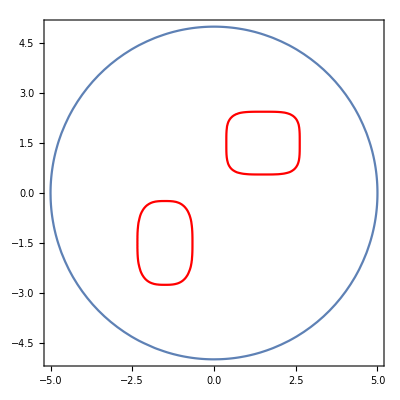

```mathematica
outEquation = x^2 + y^2 == 25;
equation1 = 0.5*Abs[-1.5 + x]^4 + Abs[-1.5 + y]^4 == 0.8;
equation2 = Abs[1.5 + x]^3 + 0.3*Abs[1.5 + y]^3 == 0.6;

Show[
	ContourPlot[x^2 + y^2 == 25, {x, -5, 5}, {y, -5, 5}], 
	ContourPlot[0.5*Abs[-1.5 + x]^4 + Abs[-1.5 + y]^4 == 0.8, {x, -5, 5}, {y, -5, 5}, ContourStyle->Red], 
	ContourPlot[Abs[1.5 + x]^3 + 0.3*Abs[1.5 + y]^3 == 0.6, {x, -5, 5}, {y, -5, 5}, ContourStyle->Red]
	]

(* Создание областей для каждого уравнения *)
regionOut = ImplicitRegion[x^2 + y^2 <= 25, {x, y}];
region1 = ImplicitRegion[0.5*Abs[-1.5 + x]^4 + Abs[-1.5 + y]^4 <= 0.8, {x, y}];
region2 = ImplicitRegion[Abs[1.5 + x]^3 + 0.3*Abs[1.5 + y]^3 <= 0.6, {x, y}];

(*  Искомая область между электронами *)
findRegion = RegionDifference[RegionDifference[regionOut, region1], region2];

outPotential = 0;
Potential1 = 5;
Potential2 = -5;
```

```mathematica
DirConditions = {
    DirichletCondition[u[x, y] == outPotential, outEquation],
    DirichletCondition[u[x, y] == Potential1, equation1],
    DirichletCondition[u[x, y] == Potential2, equation2]
}

LaplEquation = Laplacian[u[x, y], {x, y}] == 0;

result = NDSolve[{LaplEquation, DirConditions}, u, {x, y} ∈ findRegion];
```

{DirichletCondition[u[x,y]==0,x^2+y^2==25],DirichletCondition[u[x,y]==5,0.5 Abs[-1.5+x]^4+Abs[-1.5+y]^4==0.8],DirichletCondition[u[x,y]==-5,Abs[1.5+x]^3+0.3 Abs[1.5+y]^3==0.6]}

```mathematica
tempPlot = ContourPlot[u[x,y]/. First[result],{x, y} ∈ findRegion, Contours->12, ColorFunction->"BlueGreenYellow"];
eqiPlot = ContourPlot[Evaluate[u[x,y]/. result]==4,{x, y} ∈ findRegion, Contours->1, ContourStyle->Red];

Show[tempPlot, eqiPlot]
```

-Graphics-

```mathematica
findLine = DiscretizeGraphics[eqiPlot];
findLenght = RegionMeasure[findLine]
```

8.76124